```mathematica
Off[Inverse::luc]
Off[LinearSolve::luc]
workingdirectory=$HomeDirectory<>"/kette_repo/ComptonLIT/mul_helion_miwchan/LITstate";
SetDirectory[workingdirectory];

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];{(Transpose[transf].DiagonalMatrix[μ^(-1/2)])}]

decompose[threshold_,norm_,ham_]:= Block[{},Oμ=normreg[threshold,norm][[1]];{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];];
```

Norm EV_max = 8.0302×10^6    Norm EV_min = 4.44663×10^-12     Norm EV threshold = 5.28178×10^-7

Condition number ℕ_ij = 7.26537×10^11

EV_full(ℍ) = {1.30202,1.18585,0.521011,-7.61657}

EV_(EV (𝟙) > threshold)(ℍ) = {1.30201,1.18585,0.520949,-7.6157}

Norm EV_max = 1.37721×10^10    Norm EV_min = 2.27931×10^-7     Norm EV threshold = 4.44663×10^-12

Condition number ℕ_ij = 7.50109×10^12

EV_full(ℍ) = {0.616548,0.462737,0.404728,-139.904}

EV_(EV (𝟙) > threshold)(ℍ) = {0.616547,0.462737,0.404728,-99.1339}

Norm EV_max = 1.37721×10^10    Norm EV_min = 5.28178×10^-7     Norm EV threshold = 2.27931×10^-7

Condition number ℕ_ij = 6.89463×10^9

EV_full(ℍ) = {0.820166,0.623318,0.463691,0.40488}

EV_(EV (𝟙) > threshold)(ℍ) = {0.820166,0.623317,0.46369,0.40488}

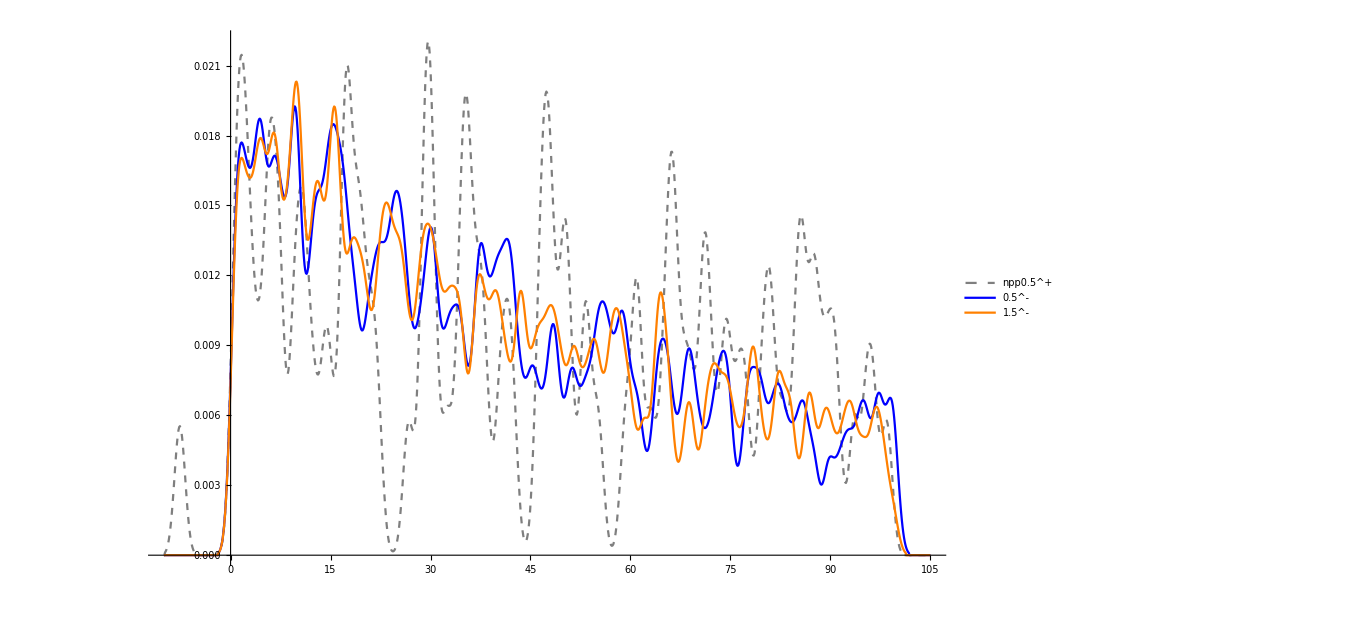

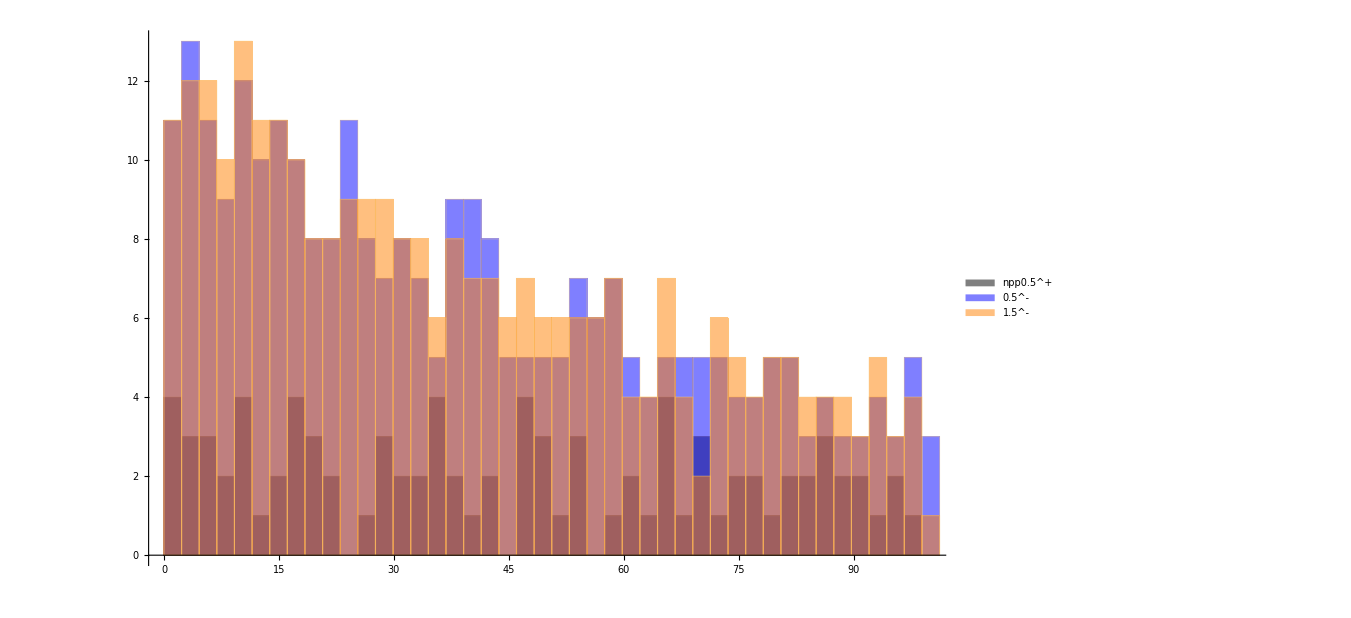

```mathematica
ℏc=197.32858;
Mnucl=(938.2796+939.5731)/2.;
bastypes={"npp0.5^+","0.5^-","1.5^-"};
histInput={};

Do[
NormHamMat=ReadList["./mat_"<>bastypes[[n]],Number];

JbasisDim=NormHamMat[[1]];

norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];
evnbare=Sort[Eigenvalues[norm],#1>#2&];
Print["Norm EV_max = ",evnbare[[1]],"    Norm EV_min = ",evnbare[[-1]],"     Norm EV threshold = ",N[thr]];
thr=Max[10^-14,evnbare[[-1]]];

ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
decompose[thr,norm,ham];
evhamunnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];

renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];
ham=renorm.ham.renorm;norm=renorm.norm.renorm;
evhamnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];

evn=Eigenvalues[norm];

Print["Condition number ℕ_ij = ",Abs[Max[evn]/Min[evn]]];
Print["EV_full(ℍ) = ",evhamnorm[[-4;;]]];
Print["EV_(EV (𝟙) > threshold)(ℍ) = ",Sort[λs,Re[#1]>Re[#2]&][[-4;;]]];

thh=100;
AppendTo[histInput,{Select[Re[evhamunnorm],Abs[#]<thh&],Re[Select[evhamnorm,Abs[#1]<thh&]]}];

,{n,Range[Length[bastypes]]}]

histInput[[1,All]];
SmoothHistogram[histInput[[All,1]],0.8,ImageSize->1000,PlotRange->{{-10,1.05 thh},Automatic},PlotStyle->{{Black,Dashed,Thick,Opacity[0.5]},Blue,Orange},PlotLegends->bastypes]
Histogram[histInput[[All,1]],{2.3},ImageSize->1000,PlotRange->{{0,thh},Automatic},ChartStyle->{Black,Blue,Orange},ChartLegends->bastypes]
```

```mathematica
Inhomo=ReadList["~/kette_repo/ComptonLIT/mul_helion_miwchan_test/tmp_0/MATOUT",Number];
dim=Dimensions[Inhomo];
```

ReadList::noopen: Cannot open ~/kette_repo/ComptonLIT/mul_helion_miwchan_test/tmp_0/MATOUT.

```mathematica
Sqrt[dim/2]
```

{}

```mathematica
COEF=Normalize[ReadList["~/kette_repo/ComptonLIT/mul_helion_miwchan_test_1/he3/COEFF",Number]];
COEFN=Normalize[ReadList["~/kette_repo/ComptonLIT/mul_helion_miwchan_test_1/he3/COEFF_NORMAL",Number]];
```

ReadList::noopen: Cannot open ~/kette_repo/ComptonLIT/mul_helion_miwchan_test_1/he3/COEFF.

ReadList::noopen: Cannot open ~/kette_repo/ComptonLIT/mul_helion_miwchan_test_1/he3/COEFF_NORMAL.

```mathematica
ListPlot[{COEF,COEFN},PlotStyle->{Blue,Orange},PlotLegends->{"Z^TℕZ=𝟙","Z=𝟙^(-1/2)Z"},AxesLabel->{"basis-vector index","expansion coefficient"},ImageSize->750,PlotRange->{{0,50},Automatic}]
```

-Graphics-